```mathematica
SetOptions[EvaluationNotebook[],CellProlog:>SelectionMove[NextCell[CellStyle->"Input"],All,Cell]]
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{newtxtext}\\usepackage{newtxmath}"}];
texStyle = {FontFamily->"Times New Roman",FontSize->18};
```

```mathematica
Γ = 0.1;
Fr = 0.025;
LZ = 0.0035;
```

```mathematica
reg =0.01;
```

```mathematica
vAz2[x_]=Cos[2Pi x]^2+reg;
kz[x_]=1/(Γ Sqrt[vAz2[x]]);
bybase[x_,t_]=I Sin[(2Pi x)]Exp[-I t];
by[x_,Z_,t_]=bybase[x,t]Exp[I kz[x]Z/Fr];
v[x_,Z_,t_]=-by[x,Z,t];
xi[x_,Z_,t_]=v[x,Z,t]/(-I);
```

```mathematica
xi[x,Z,t]==Sin[(2Pi x)]Exp[-I t]Exp[I kz[x]Z/Fr]
```

True

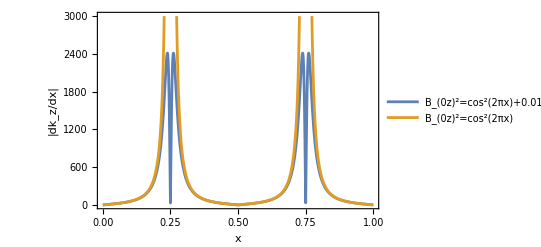

```mathematica
Plot[{Evaluate[Abs[D[kz[x],x]]],Evaluate[Abs[D[1/(Γ Sqrt[vAz2[x]-reg]),x]]]},{x,0,1},PlotRange->{All,{0,3000}},FrameLabel->{"x","|dk_z/dx|"},Frame->True,PlotLegends->{"B_(0z)^2=cos^2(2πx)+"<>ToString[reg],"B_(0z)^2=cos^2(2πx)"}]
```

```mathematica
matplotlibPurples={RGBColor[{0.9882352941176471, 0.984313725490196, 0.9921568627450981}],RGBColor[{0.9372549019607843, 0.9294117647058824, 0.9607843137254902}],RGBColor[{0.8549019607843137, 0.8549019607843137, 0.9215686274509803}],RGBColor[{0.7372549019607844, 0.7411764705882353, 0.8627450980392157}],RGBColor[{0.6196078431372549, 0.6039215686274509, 0.7843137254901961}],RGBColor[{0.5019607843137255, 0.49019607843137253, 0.7294117647058823}],RGBColor[{0.41568627450980394, 0.3176470588235294, 0.6392156862745098}],RGBColor[{0.32941176470588235, 0.15294117647058825, 0.5607843137254902}],RGBColor[{0.24705882352941178, 0., 0.49019607843137253}]};
PurplesList=matplotlibPurples[[2;;7]];
saturate=0.1;
PurplesSatList=Table[Hue[Hue[PurplesList[[i]]][[1]],Hue[PurplesList[[i]]][[2]]+ saturate,Hue[PurplesList[[i]]][[3]]],{i,1,Length[PurplesList]}];
PurplesMap=Blend[PurplesList,#]&;
PurplesSatMap=Blend[PurplesSatList,#]&;
```

```mathematica
tplot=24Pi;
tplanes=4Pi;
deltplanes=4Pi;
amp=1/10;
Zvals={0,1/3,2/3,1};
tuberadius=0.0075;
Nlines=13;
xlinel=0.04;
xliner=0.96;
linecmap =PurplesSatMap;
linecfxn[x_]:=linecmap[Sqrt[vAz2[x]]/Sqrt[(1+reg)]];
Nx=2048;
NZ=256;
profcolor=RGBColor[1, 0.25, 0.];
profthickness=0.0075;
brighnessfactor =1.35;
lightingspecs={{"Ambient",RGBColor[{0.35,0.35,0.35}]},{"Directional",RGBColor[brighnessfactor*{0.37,0.37,0.37}],ImageScaled[{2,0,2}]},{"Directional",RGBColor[brighnessfactor*{0.37,0.37,0.37}],ImageScaled[{2,2,2}]},{"Directional",RGBColor[brighnessfactor*{0.37,0.37,0.37}],ImageScaled[{0,2,2}]}};
legendxl=0.15;
legendxr=0.85;

animfunc[t_,Nx_,NZ_]:=Show[
Join[
(*Field lines*)
Table[
Graphics3D[
{
Lighting->lightingspecs(*DirectionalLight[{White,Specularity[0]},{{6,-2,0},{0,1,0}}]*)(*"Neutral"*),
linecfxn[x],
CapForm["Butt"],
Tube[
Table[
{x,amp*ReIm[xi[x,z LZ,t]][[1]],z},{z,0,1,1/NZ}
],
tuberadius
]
},
Lighting->None(*{{"Point",White,Scaled[{2,-1,1.2}]}}*)],
{x,xlinel,xliner,(xliner-xlinel)/(Nlines-1)}
],

(*Profiles*)
Table[
ParametricPlot3D[
{x,amp*ReIm[xi[x,LZ Zvals[[i]],t]][[1]],Zvals[[i]]},
{x,0,1},
PlotStyle->Directive[profcolor,Thickness[profthickness]],
PlotPoints->256
],
{i,1,If[(t>tplanes),Min[Length[Zvals],Floor[(t-tplanes)/deltplanes,1]+1],1]}
],

(*Planes*)
Table[
ParametricPlot3D[
{x,y,Zvals[[i]]},
{x,0,1},
{y,-1,1},
Mesh->None,
Lighting->{{"Ambient", White}},
PlotStyle->Directive[RGBColor[0.8200000000000001, 0.8200000000000001, 0.8200000000000001],Opacity[0.8]]
],
{i,1,If[(t>tplanes),Min[Length[Zvals],Floor[(t-tplanes)/deltplanes,1]+1],1]}
]
],
Epilog->{
Inset[
BarLegend[
{PurplesMap[#/(1+reg)]&,{0,1+reg}},
Ticks->{{0,MaTeX["0",Magnification->18/12]},{1,MaTeX["1",Magnification->18/12]}},
LegendMarkerSize->{160,8},
LegendLayout->"Row",
(*LegendLabel->MaTeX["\\lvert B_{0 z} \\rvert",Magnification->18/12],*)
LegendMargins->{None,{-100,0}},
Charting`TickSide->Left
],
{0.525,1.275}
],
Inset[
MaTeX["\\lvert B_{0 z} \\rvert",Magnification->24/12],{0.55,1.325}
]
},
Boxed->False,
Axes->True,
AxesStyle->Directive[Black,Thickness[0.005]],
ImagePadding->{{20,40},{25,70}},
Ticks->{{0,0.5,1},False,False},
AxesEdge->{{-1,-1},{1,-1},{1,1}},
AxesLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\; y","\\;\\;z"},
PlotRange->{{0,1},{-1.1 amp,1.1* amp},{0,Zvals[[-1]]}},
BoxRatios->{3.25,1,4.},
BaseStyle->texStyle]

p=animfunc[tplot,Nx,NZ]

Export[NotebookDirectory[]<>"fig3.jpg",p,ImageResolution->600]
```

-Graphics3D-

/Users/cydavid/git repos/magIGWs/fig3.jpg

```mathematica
Manipulate[animfunc[t,256,32],
{t,0,24Pi}]
```

```mathematica
frames=Table[animfunc[t,256,32],{t,0,24Pi,Pi/16}];

Export[NotebookDirectory[]<>"fig3.mp4",frames]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

/Users/cydavid/git repos/magIGWs/fig3.mp4